```mathematica
(*Malthus Model*)
(*Initialize Kernel*)
ClearAll;
(*Solve, analytically, the Malthus differential equation for exponential population growth*)
DSolve[{n'[t]==r * (n[t]),n[0]==N0},n[t],t]
```

DSolve::dsfun: ⅇ^(r t) N0 cannot be used as a function.

DSolve[{True,True},ⅇ^(r t) N0,t]

```mathematica
(*Convert solution to function*)
n[t_]:=N0*E^(r t)
realzero=n[t]/. Solve[n'[x]==0,Reals];
```

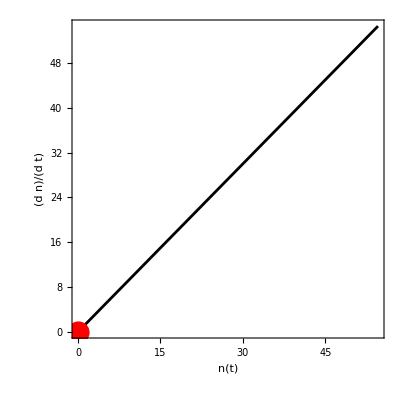

```mathematica
(*Phase Portrait (in red, unstable fixed points, in black stable fixed points)*)
Show[ParametricPlot[{n[t]/.{r->1,N0->1},n'[t]/.{r->1,N0->1}},{t,0,4},PlotStyle->Black], Epilog->{PointSize[0.04],Red,Tooltip[#,#[[1]]]&@Point[{realzero[[1]],0}]},AspectRatio->1,Frame->True,FrameLabel->(Style[#,14]&/@{"n(t)","(d n)/(d t)"})]
```

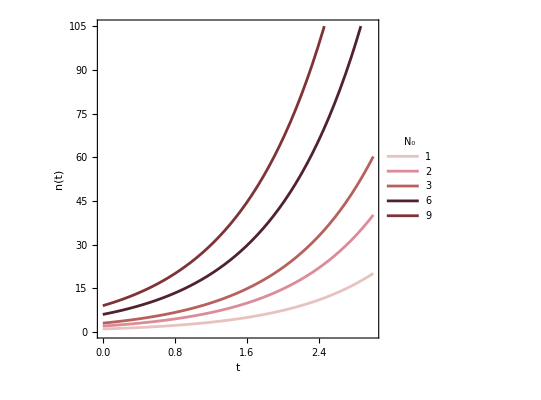

```mathematica
(*Plot n(t) versus t for r=1 and N0 ranging 1 to 4*)Plot[Evaluate@Table[n[t]/.r->1,{N0,{1,2,3,6,9}}],{t,0,3},Frame->True,PlotLegends->LineLegend[Table[N0,{N0,{1,2,3,6,9}}],LegendLabel->Subscript[N, 0]],AspectRatio->1,FrameLabel-> {"t","n(t)"},PlotStyle->ColorData[62,"ColorList"]]
```